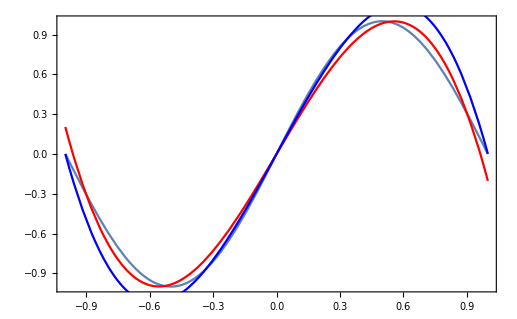

0.00878023

0.0394032

```mathematica
f[x_]:=Sin[π x];
n=3;
a=-1;
b=1;
A=Table[∫_a^b If[k-1+j-1==0,1,x^(k-1+j-1)]ⅆx,{k,1,n+1},{j,1,n+1}];
α=Table[a[i-1],{i,1,n+1}];
bb=Table[∫_a^b f[x] If[k-1==0,1,x^(k-1)]ⅆx,{k,1,n+1}];
α=α/.Solve[A.α==bb,α][[1]];
p[x_]:=α.Table[If[i-1==0,1,x^(i-1)],{i,1,n+1}];
xi[i_Integer]:=a+i(b-a)/n;
L[j_Integer,x_]:=(∏_(k=0)^(j-1) (x-xi[k])/(xi[j]-xi[k])) (∏_(k=j+1)^n (x-xi[k])/(xi[j]-xi[k]));
ip[x_]:=∑_(j=0)^n f[xi[j]] L[j,x];
p1=Plot[f[x],{x,a,b},DisplayFunction->Identity];
p2=Plot[p[x],{x,a,b},DisplayFunction->Identity,PlotStyle->RGBColor[1,0,0]];
p3=Plot[ip[x],{x,a,b},DisplayFunction->Identity,PlotStyle->RGBColor[0,0,1]];
Show[p1,p2,p3,DisplayFunction->$DisplayFunction,Frame->True]
E21=∫_a^b (f[x]-p[x])^2ⅆx//N
E22=∫_a^b (f[x]-ip[x])^2ⅆx//N
```